```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Load core activity, converting all date/times into DateObjects*)
```

```mathematica
coreActivity = Import["activity.tsv", "TSV"];coreActivity[[Range[2, Length[coreActivity]],3]]=(DateObject[StringDrop[#,-8]] &)/@coreActivity[[Range[2, Length[coreActivity]],3]];coreActivity[[Range[2, Length[coreActivity]],4]]=(DateObject[StringDrop[#,-8]] &)/@coreActivity[[Range[2, Length[coreActivity]],4]];
```

```mathematica
startTime=Sort[coreActivity[[Range[2, Length[coreActivity]],3]]][[1]]
```

Sun 29 Nov 2015 12:55:00

```mathematica
endTime=Reverse[Sort[coreActivity[[Range[2, Length[coreActivity]],4]]]][[1]]
```

Fri 4 Dec 2015 18:23:00

```mathematica
UnitConvert[endTime-startTime,MixedRadix["Days","Hours","Minutes","Seconds"]]
```

55286.82121×10^-12

```mathematica
(*Exclude job flows that failed to start from prep activity*)
```

```mathematica
prepActivity=Select[coreActivity[[Range[2,Length[coreActivity]]]], #[[2]]=="prep" && #[[8]]==0&];
```

```mathematica
alignActivity=Select[coreActivity[[Range[2,Length[coreActivity]]]], #[[2]]=="align" && #[[8]]==0&];
```

```mathematica
prepPiece=Total[Piecewise[{{1, QuantityMagnitude[#[[3]]-startTime]≤x≤ QuantityMagnitude[#[[4]]-startTime]}}]&/@prepActivity] *80;
```

```mathematica
alignPiece=Total[Piecewise[{{1, QuantityMagnitude[#[[3]]-startTime]≤x≤ QuantityMagnitude[#[[4]]-startTime]}}]&/@alignActivity]*2560;
```

```mathematica
(*First plot is of number of active cores in time during preprocess job flows; second plot is of number of active cores in time during align job flows*)
```

```mathematica
interval=.01; dateRange=Range[0, QuantityMagnitude[endTime-startTime], interval];
```

```mathematica
imagePadding={{70,30},{50,30}};
```

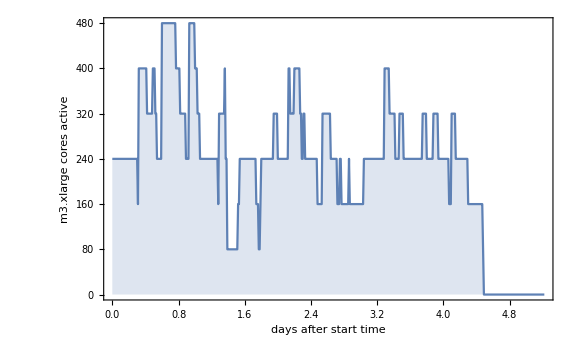

```mathematica
prepPlot=ListPlot[Transpose[{dateRange,(prepPiece/.x->#)&/@dateRange}], Joined->True, Filling->Axis, BaseStyle->{FontName->"Helvetica", FontSize->15},Frame->True, ImageSize->Large, ImagePadding->imagePadding, FrameLabel->{{"m3.xlarge cores active", ""}, {"days after start time","a) number of rented worker processing cores during preprocessing"}}]
```

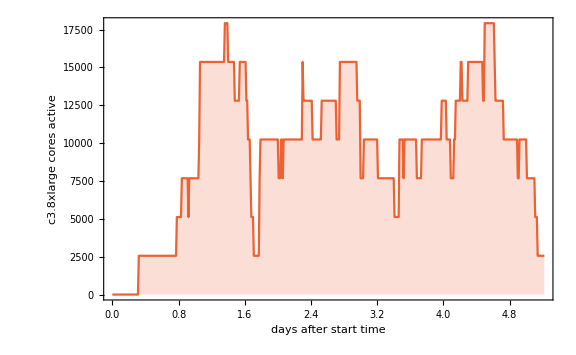

```mathematica
alignPlot=ListPlot[Transpose[{dateRange,(alignPiece/.x->#)&/@dateRange}], Joined->True, Filling->Axis, BaseStyle->{FontName->"Helvetica", FontSize->15},Frame->True, ImageSize->Large, ImagePadding->imagePadding,PlotStyle->ColorData[97,"ColorList"][[4]],FrameLabel->{{"c3.8xlarge cores active", ""}, {"days after start time","b) number of rented worker processing cores during alignment"}}]
```

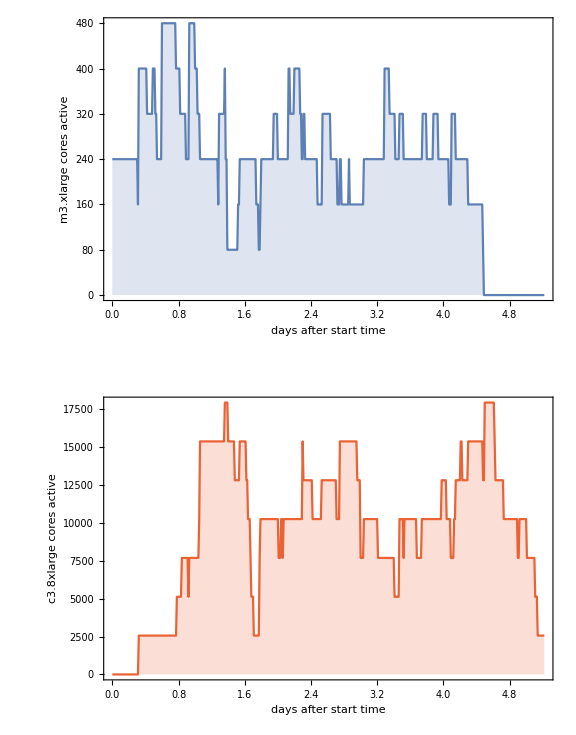

```mathematica
corePlot=GraphicsGrid[{{prepPlot},{alignPlot}}, ImageSize->Large]
```

```mathematica
Export["cores.pdf",corePlot]
```

cores.pdf

```mathematica
costs = Import["costs.csv", "CSV"]
```

{{Service,Amazon Elastic Compute Cloud,Amazon Elastic MapReduce,Amazon Simple Storage Service,Amazon Simple Queue Service,Amazon SimpleDB,Daily Total},{Service Total,16438.8,10988.,941.147,0.188414,0.00032373,28368.1},{2015-12-04,3540.01,2447.88,259.38,0.0584892,0.00007988,6247.33},{2015-12-03,2978.24,2070.72,269.756,0.0440118,0.00008047,5318.76},{2015-12-02,3543.74,2617.14,182.314,0.0576925,0.00007993,6343.25},{2015-12-01,4120.24,2513.98,189.469,0.00480737,0.,6823.69},{2015-11-30,2256.6,1338.27,40.228,0.0234128,0.00008345,3635.12}}

```mathematica
data=costs[[2,Range[2,4]]];data=Append[data, costs[[2,5]]+costs[[2,6]]];
labels={"EC2","EMR","S3","other"};
```

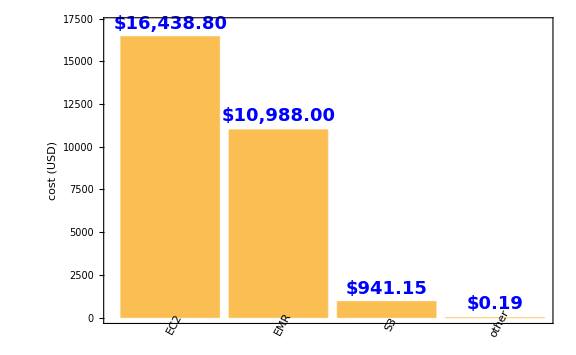

```mathematica
costPlot=Show[BarChart[data,ChartLabels->Placed[labels,Below,Rotate[#,Pi/2.9]&],BaseStyle->{FontName->"Helvetica", FontSize->15, Black}, ImageSize->Large, Frame->True,FrameLabel->{{"cost (USD)", ""},{"", "total costs of aligning GTEx RNA-seq data by Amazon service"}}, FrameTicks->{None, True}], Graphics[Text[Style["$16,438.80", Bold, Blue, FontSize->18], {1,17200}]],Graphics[Text[Style["$10,988.00", Bold, Blue, FontSize->18], {2,11800}]],
Graphics[Text[Style["$941.15", Bold, Blue, FontSize->18], {3,1700}]],
Graphics[Text[Style["$0.19", Bold, Blue, FontSize->18], {4,800}]], ImageSize->Large]
```

```mathematica
Export["costs.pdf",costPlot]
```

costs.pdf